```mathematica
Clear[ϵ]
```

```mathematica
(1/(50*365))/((1/(50*365))+1/7)
```

7/18257

```mathematica
S=(1/R)-(2p/((R-1)+√((R-1)^2+4*R*p)))
```

1/R-(2 p)/(-1+R+√((-1+R)^2+4 p R))

```mathematica
V=(ϵ*(R-1)+ϵ*√((R-1)^2+4*R*p))/(2*R)
```

((-1+R)/1000+(√((-1+R)^2+4 p R))/1000)/(2 R)

```mathematica
ϵ=1/1000
```

1/1000

```mathematica
Solve[(1-R S+R V+ϵ)^2-4 (R V+ϵ-R S ϵ)==0,p]
```

{{p→1/(1004006004001 R^2)(-7984008000 R+9002995001 R^2-1002001000 R^3-60 √1110 √(-987049950012999 R^2+2975038037975003 R^3-2988986014010997 R^4+1000997998001001 R^5))},{p→1/(1004006004001 R^2)(-7984008000 R+9002995001 R^2-1002001000 R^3+60 √1110 √(-987049950012999 R^2+2975038037975003 R^3-2988986014010997 R^4+1000997998001001 R^5))}}

```mathematica
Clear[p]
```

```mathematica
g[R_]:=1/(1004006004001 R^2)(-7984008000 R+9002995001 R^2-1002001000 R^3+60 √1110 √(-987049950012999 R^2+2975038037975003 R^3-2988986014010997 R^4+1000997998001001 R^5))
```

```mathematica
h[R_]:=g[R+1]
```

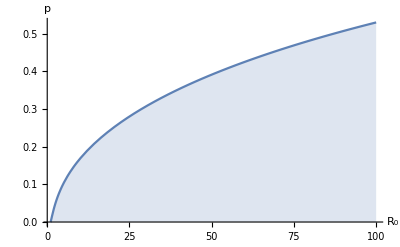

```mathematica
Plot[g[R],{R,0,100},Filling->Bottom,AxesLabel->{Subscript[R, 0],p},PlotRange->All]
```

LogLinearPlot::invpr: Value of option PlotRange should be positive in the scaled dimensions.

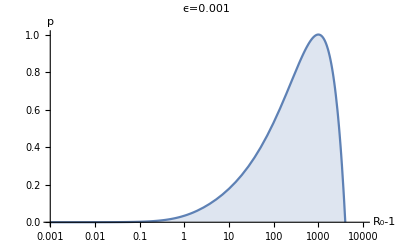

```mathematica
LogLinearPlot[h[R],{R,0.001,10000},Filling->Bottom,AxesLabel->{"R_0-1",p},PlotRange->{{0,10000},{0,1}},PlotLabel->"ϵ=0.001"]
```

```mathematica
Export["C:\\Users\\Roger Zhang\\Documents\\GitHub\\RogerZhang\\July_6th\\Figures\\epsilon_0.001",%36,"PDF"]
```

C:\Users\Roger Zhang\Documents\GitHub\RogerZhang\July_6th\Figures\epsilon_0.001